```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];
```

```mathematica
top:=Module[{list,count,img,list2,list3,tmp,d1},(* top *)
list=Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,tmp,d4},(* bottom *)
list=Reverse@Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha,fun,vis,viss,vs,viss2,vs2,mean},
alpha=alpha0;
MapIndexed[(alpha[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha}],InterpolationOrder->1];
vis=Block[{f=fun},renderslices[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
vs=Table[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
vs2=Table[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}];
mean=Mean[{vs,vs2}]
]
Visibility[fun_]:=Module[{vis,viss,vs,viss2,vs2,mean},
vis=Block[{f=fun},renderslices[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
vs=ParallelTable[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
vs2=ParallelTable[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}];
mean=Mean[{vs,vs2}]
]
```

```mathematica
records={};
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
target={0.1,0.3,0.6};
epsilon=0.001;
stepsize=0.1;
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,22}];
t2-t1
iteration
```

7.2782675

5

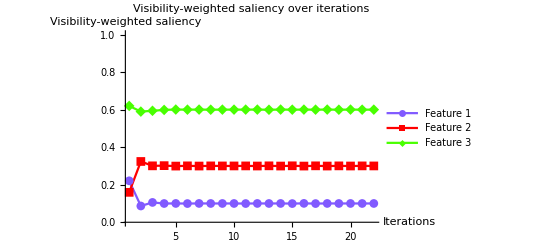

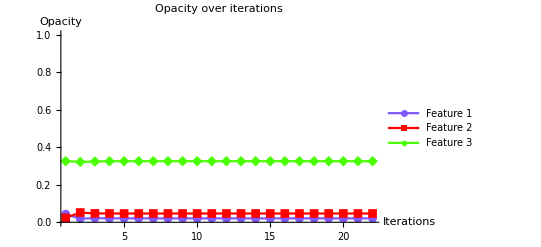

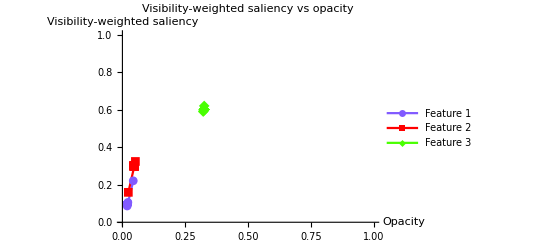

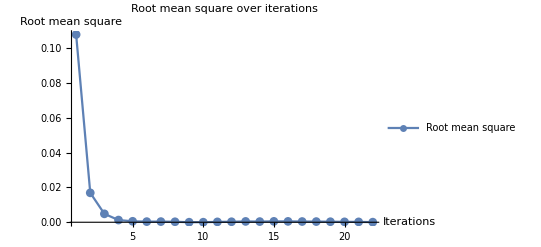

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps
1 | 0.220811
0.159342
0.619807 | 0.0431373
0.0235294
0.32549 | 0.10766 | -0.0241621
0.0281317
-0.0039614
2 | 0.0866154
0.323786
0.589561 | 0.0189751
0.0516611
0.321529 | 0.016871 | 0.00267693
-0.0047572
0.00208774
3 | 0.105608
0.300533
0.593822 | 0.0216521
0.0469039
0.323617 | 0.00482695 | -0.00112151
-0.000106583
0.00123564
4 | 0.0998731
0.301582
0.598507 | 0.0205306
0.0467973
0.324852 | 0.00125793 | 0.000025376
-0.000316366
0.000298589
5 | 0.100194
0.299239
0.600529 | 0.0205559
0.0464809
0.325151 | 0.000546753 | -0.0000387956
0.000152226
-0.000105805
6 | 0.0996274
0.300481
0.599854 | 0.0205171
0.0466332
0.325045 | 0.000361179 | 0.0000745133
-0.0000961554
0.0000292567
7 | 0.100222
0.299459
0.600281 | 0.0205917
0.046537
0.325074 | 0.000374702 | -0.0000444002
0.000108241
-0.0000562191
8 | 0.100055
0.300287
0.59962 | 0.0205473
0.0466453
0.325018 | 0.000276935 | -0.0000110726
-0.0000573884
0.0000760731
9 | 0.100026
0.299969
0.599967 | 0.0205362
0.0465879
0.325094 | 0.0000303372 | -5.25254×10^-6
6.26283×10^-6
6.60523×10^-6
10 | 0.100027
0.299972
0.599963 | 0.0205309
0.0465941
0.325101 | 0.0000311251 | -5.44004×10^-6
5.68108×10^-6
7.37456×10^-6
11 | 0.0996887
0.300133
0.60014 | 0.0205255
0.0465998
0.325108 | 0.000211579 | 0.0000622693
-0.0000266271
-0.0000280253
12 | 0.100165
0.299579
0.600218 | 0.0205878
0.0465732
0.32508 | 0.000289608 | -0.0000329585
0.0000841452
-0.0000435668
13 | 0.100021
0.300549
0.599392 | 0.0205548
0.0466573
0.325036 | 0.00047294 | -4.11476×10^-6
-0.000109799
0.000121523
14 | 0.100157
0.299459
0.600345 | 0.0205507
0.0465475
0.325158 | 0.000381447 | -0.0000314703
0.000108163
-0.0000690702
15 | 0.0995418
0.300697
0.599723 | 0.0205192
0.0466557
0.325089 | 0.000507271 | 0.0000916438
-0.000139355
0.0000553215
16 | 0.100512
0.299322
0.600129 | 0.0206109
0.0465163
0.325144 | 0.000496139 | -0.00010231
0.000135677
-0.0000257469
17 | 0.0995591
0.300554
0.599848 | 0.0205086
0.046652
0.325118 | 0.000418219 | 0.0000881867
-0.000110877
0.0000303025
18 | 0.100185
0.29945
0.600327 | 0.0205967
0.0465411
0.325149 | 0.000384381 | -0.0000369804
0.000109958
-0.0000653563
19 | 0.099988
0.300364
0.59961 | 0.0205598
0.0466511
0.325083 | 0.000308361 | 2.39508×10^-6
-0.0000728616
0.0000780759
20 | 0.100111
0.299663
0.600188 | 0.0205622
0.0465782
0.325162 | 0.000231622 | -0.0000221736
0.0000673483
-0.0000375555
21 | 0.100003
0.300237
0.599722 | 0.02054
0.0466456
0.325124 | 0.000211193 | -6.26262×10^-7
-0.0000474468
0.0000556839
22 | 0.100057
0.299986
0.599919 | 0.0205394
0.0465981
0.32518 | 0.0000579552 | -0.0000114216
2.75719×10^-6
0.0000162789

```mathematica
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>"saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>"opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>"rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>"table_fixed.png",table1];
(*path1=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

```mathematica
(*alpha0[[#]]&/@index0
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0]*)
(*(*first order newton*)
target={0.1,0.3,0.6};
stepsize=0.1;
previous={{0,0,0},{0,0,0}};
list=Table[Module[{peaks,mean,steps,rms,f1,f0,diff,square,derivative,xx,dx,yy,df,factor},
mean=visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
derivative=2*(mean-target);
square=(mean-target)^2;
If[Norm[First@previous]>0,{f1,f0,xx,yy}=previous,{f1,f0,xx,yy}={derivative,square,peaks,mean}];
(*diff=mean-y1;
steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,(target-mean)*(peaks-x1)/(mean-y1)*stepsize,2*(target-mean)*stepsize];*)
(*dx=peaks-xx;
df=If[Product[dx[[i]],{i,Length[dx]}]≠0,(mean-yy)/dx,1];*)
(*derivative=derivative*df;*)
diff=derivative-f1;
previous={derivative,square,peaks,mean};
df=If[Product[diff[[i]],{i,Length[diff]}]≠0,-(square-f0)/diff*stepsize,-derivative*stepsize];
dx=-derivative*stepsize;
steps=Table[If[Abs[dx[[i]]]>Abs[df[[i]]],dx[[i]],df[[i]]],{i,Length[mean]}];
(*steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,-derivative*(peaks-xx)/diff*stepsize,-derivative*stepsize];*)
(*steps=-derivative*stepsize;*)
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
{mean,peaks,rms,steps,dx,df,Table[Abs[df[[i]]]>Abs[dx[[i]]],{i,Length[dx]}]}
],{30}];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
stepsize=0.1;
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,7}];
t2-t1
iteration
```

8.3122577

4

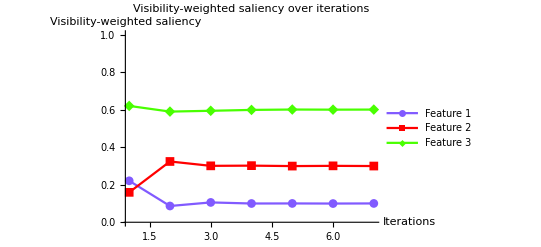

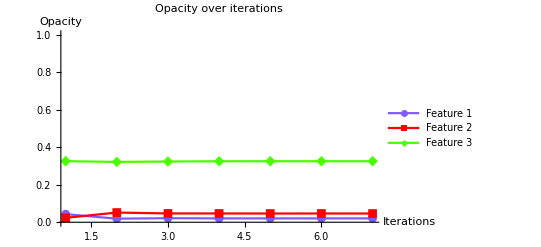

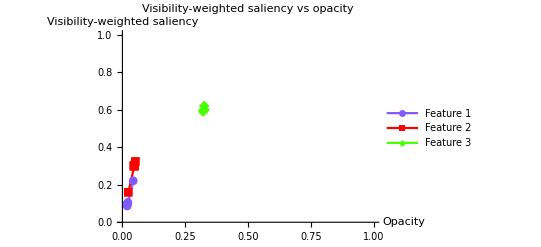

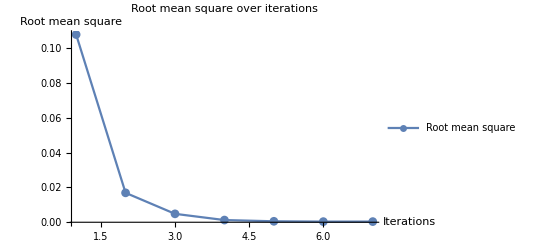

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.220811
0.159342
0.619807 | 0.0431373
0.0235294
0.32549 | 0.10766 | -0.0241621
0.0281317
-0.0039614 | 1
2 | 0.0866154
0.323786
0.589561 | 0.0189751
0.0516611
0.321529 | 0.016871 | 0.00267693
-0.0047572
0.00208774 | 1
3 | 0.105608
0.300533
0.593822 | 0.0216521
0.0469039
0.323617 | 0.00482695 | -0.00112151
-0.000106583
0.00123564 | 1
4 | 0.0998731
0.301582
0.598507 | 0.0205306
0.0467973
0.324852 | 0.00125793 | 0.000025376
-0.000316366
0.000298589 | 1
5 | 0.100194
0.299239
0.600529 | 0.0205559
0.0464809
0.325151 | 0.000546753 | -0.0000387956
0.000152226
-0.000105805 | 1
6 | 0.0996274
0.300481
0.599854 | 0.0205171
0.0466332
0.325045 | 0.000361179 | 0.0000745133
-0.0000961554
0.0000292567 | 1
7 | 0.100222
0.299459
0.600281 | 0.0205917
0.046537
0.325074 | 0.000374702 | -0.0000444002
0.000108241
-0.0000562191 | 1

```mathematica
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>"saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>"opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>"rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>"table_parallelsearch.png",table2];
(*path2=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
stepsize=0.1;
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,7}];
t2-t1
iteration
```

4.9181577

4

```mathematica
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>"saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>"opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>"rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>"table_linesearch.png",table3];
(*path3=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.220811
0.159342
0.619807 | 0.0431373
0.0235294
0.32549 | 0.10766 | -0.0241621
0.0281317
-0.0039614 | 1
2 | 0.0866154
0.323786
0.589561 | 0.0189751
0.0516611
0.321529 | 0.016871 | 0.00267693
-0.0047572
0.00208774 | 1
3 | 0.105608
0.300533
0.593822 | 0.0216521
0.0469039
0.323617 | 0.00482695 | -0.00112151
-0.000106583
0.00123564 | 1
4 | 0.0998731
0.301582
0.598507 | 0.0205306
0.0467973
0.324852 | 0.00125793 | 0.000025376
-0.000316366
0.000298589 | 1
5 | 0.100194
0.299239
0.600529 | 0.0205559
0.0464809
0.325151 | 0.000546753 | -0.0000387956
0.000152226
-0.000105805 | 1
6 | 0.0996274
0.300481
0.599854 | 0.0205171
0.0466332
0.325045 | 0.000361179 | 0.0000745133
-0.0000961554
0.0000292567 | 1
7 | 0.100222
0.299459
0.600281 | 0.0205917
0.046537
0.325074 | 0.000374702 | -0.0000444002
0.000108241
-0.0000562191 | 1

```mathematica
recordxml=NotebookDirectory[]<>"~images\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

nucleon_weak_red→{{7.2782675,5,{0.0205394,0.0465981,0.32518}},{8.3122577,4,{0.0205917,0.046537,0.325074}},{4.9181577,4,{0.0205917,0.046537,0.325074}}}

```mathematica
range=Range[0,1,0.1];
coordinates=Flatten[Table[{range[[i]],range[[j]],range[[k]]},{i,Length[range]},{j,Length[range]},{k,Length[range]}],2];
Length[coordinates]
Clear[f];
CloseKernels[];
LaunchKernels[8];
searchspace=ParallelTable[Module[{peaks,mean,rms},
peaks=coordinates[[index]];
mean=VisibilitySaliency[peaks];
rms=RootMeanSquare[mean-target];
{mean,peaks,rms}
],{index,Length[coordinates]}];
```

1331

```mathematica
transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=Table[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path2,path3};
plotlegends={{"Fixed step size"},{"Adaptive step size with parallel search"},{"Adaptive step size with line search"}};
pointplots=Table[ListPointPlot3D[paths[[i]],PlotStyle->{chartcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=Table[ListPointPlot3D[paths[[i]],PlotStyle->{chartcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function as density in search space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],pointplots[[3]],lineplots[[1]],lineplots[[2]],lineplots[[3]],PlotLabel->"Gradient descent in search space",ViewPoint->vec]
Export[NotebookDirectory[]<>"searchspace.png",sp];
Export[NotebookDirectory[]<>"searchspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=Table[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=Table[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=Table[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[NotebookDirectory[]<>"densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],NotebookDirectory[]<>"optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],NotebookDirectory[]<>"optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],NotebookDirectory[]<>"optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics3D-

-Graphics3D-

-Graphics-

-Graphics-